```mathematica
(* defination *)
SU3:={"r","g","b"};
SU3B:={"R","G","B"};
Core:={{1/2,1/3,{SU3[[1]]}},{-1/2,1/3,{SU3[[2]]}},{0,-2/3,{SU3[[3]]}}};
CoreB:={{-1/2,-1/3,{SU3B[[1]]}},{1/2,-1/3,{SU3B[[2]]}},{0,2/3,{SU3B[[3]]}}};

(* bases generator *)
IndexRoot[rootdiagram_,I3_,Y_]:=Module[{roots=rootdiagram,x=I3,y=Y},
For[find=1,find≤Length[roots],find++,
If[roots[[find,1]]==x && roots[[find,2]]==y,Return[find]]
];
Return[0];
]

ProductBasis[basiset_,SU3_]:=Module[{bases=basiset,su3=SU3},
set={};
For[term=1,term≤Length[bases],term++,
set=Join[set,{bases[[term]]<>su3}];
];
Return[set];
]

ProductTriplet[rootdiagram_]:=Module[{roots=rootdiagram},
diagram={};
For[su=1,su≤Length[SU3],su++,
For[i=1,i≤Length[roots],i++,
I3=roots[[i,1]]+Core[[su,1]];
Y=roots[[i,2]]+Core[[su,2]];
index=IndexRoot[diagram,I3,Y];
Basis=ProductBasis[roots[[i,3]],Core[[su,3,1]]];
If[index==0,
diagram=Join[diagram,{{I3,Y,Basis}}],
diagram[[index,3]]=Join[diagram[[index,3]],Basis];
]]
];
Return[diagram];
]

ProductTripletB[rootdiagram_]:=Module[{roots=rootdiagram},
diagram={};
For[sub=1,sub≤Length[SU3B],sub++,
For[j=1,j≤Length[roots],j++,
I3=roots[[j,1]]+CoreB[[sub,1]];
Y=roots[[j,2]]+CoreB[[sub,2]];
index=IndexRoot[diagram,I3,Y];
Basis=ProductBasis[roots[[j,3]],CoreB[[sub,3,1]]];
If[index==0,
diagram=Join[diagram,{{I3,Y,Basis}}],
diagram[[index,3]]=Join[diagram[[index,3]],Basis];
]]
];
Return[diagram];
]

(* wave functions generator *)
OperatorA12[]

(* plot tools *)
RootWeightPlot[rootdiagram_]:=Module[{roots=rootdiagram},
diagram={};
For[len=1,len≤Length[roots],len++,
diagram=Join[diagram,{{roots[[len,1]],roots[[len,2]]}}];
];
adjacency=Table[0,{x,Length[diagram]},{y,Length[diagram]}];
For[adj1=1,adj1≤Length[diagram],adj1++,
For[adj2=1,adj2≤Length[diagram],adj2++,
distance=((diagram[[adj1,1]]-diagram[[adj2,1]])^2+(diagram[[adj1,2]]-diagram[[adj2,2]])^2)^(1/2);
If[distance==1 || distance==(5/4)^(1/2),
adjacency[[adj1,adj2]]=1;
]
]];
Print[ListPlot[diagram,PlotStyle->PointSize[Large]]];
Print[AdjacencyGraph[adjacency,GraphLayout->"SpringEmbedding"]];
]

SU3WFBuilder[configuration_,symmetry_]:=Module[{conf=configuration,sym=symmetry},
diagram={};
If[conf[[1]]=="q",diagram=Core,diagram=CoreB];
For[quark=2,quark≤Length[conf],quark++,
If[conf[[quark]]=="q",diagram=ProductTriplet[diagram],diagram=ProductTripletB[diagram]]
];
Print[diagram];
RootWeightPlot[diagram];
]
```

OperatorA12[]

{{3/2,1,{rrr}},{1/2,1,{grr,rgr,rrg}},{1,0,{brr,rbr,rrb}},{-1/2,1,{ggr,grg,rgg}},{0,0,{bgr,gbr,brg,rbg,grb,rgb}},{1/2,-1,{bbr,brb,rbb}},{-3/2,1,{ggg}},{-1,0,{bgg,gbg,ggb}},{-1/2,-1,{bbg,bgb,gbb}},{0,-2,{bbb}}}

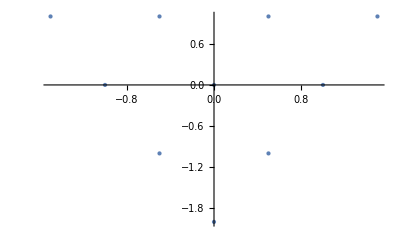

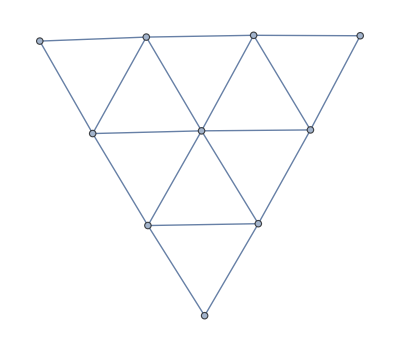

{{0,0,{rRrR,gGrR,bBrR,rGgR,rBbR,gRrG,rRgG,gGgG,bBgG,gBbG,bRrB,bGgB,rRbB,gGbB,bBbB}},{-1,0,{gRrR,rRgR,gGgR,bBgR,gBbR,gRgG,bRgB,gRbB}},{-1/2,-1,{bRrR,bGgR,rRbR,gGbR,bBbR,bRgG,gRbG,bRbB}},{1,0,{rGrR,rRrG,gGrG,bBrG,rGgG,rBbG,bGrB,rGbB}},{1/2,-1,{bGrR,rGbR,bRrG,bGgG,rRbG,gGbG,bBbG,bGbB}},{1/2,1,{rBrR,gBrG,rBgG,rRrB,gGrB,bBrB,rGgB,rBbB}},{-1/2,1,{gBrR,rBgR,gBgG,gRrB,rRgB,gGgB,bBgB,gBbB}},{-2,0,{gRgR}},{-3/2,-1,{bRgR,gRbR}},{-3/2,1,{gBgR,gRgB}},{-1,-2,{bRbR}},{0,-2,{bGbR,bRbG}},{2,0,{rGrG}},{3/2,-1,{bGrG,rGbG}},{3/2,1,{rBrG,rGrB}},{1,-2,{bGbG}},{1,2,{rBrB}},{0,2,{gBrB,rBgB}},{-1,2,{gBgB}}}

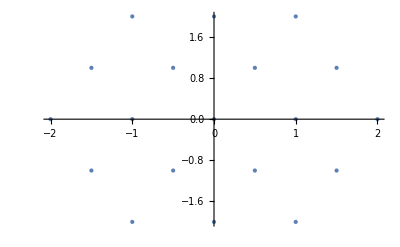

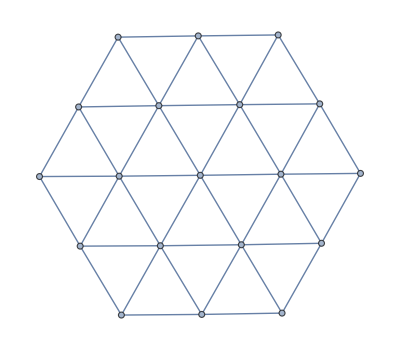

```mathematica
SU3WFBuilder[{"q","q","q"},{"A","S"}]
SU3WFBuilder[{"q","q̄","q","q̄"},{"A","S"}]
```